```mathematica
SetDirectory["C:\\anaconda32\\Work\\OnlineModel\\SimulationFramework\\Examples\\FEBE_best_longitudinal"]
```

C:\anaconda32\Work\OnlineModel\SimulationFramework\Examples\FEBE_best_longitudinal

```mathematica
SetDirectory["\\\\apclara1\\jkj62\\OnlineModel\\SimulationFramework\\Examples\\test"]
```

\\apclara1\jkj62\OnlineModel\SimulationFramework\Examples\test

```mathematica
Import["./CLA-S07-DIA-BPM-03.hdf5","/Parameters/"]
```

Import::nffil: File not found during Import.

$Failed

```mathematica
Import["./CLA-S07-DIA-BPM-03.hdf5","/beam/columns"]
```

Import::nffil: File not found during Import.

$Failed

```mathematica
{x,y,z,cpx,cpy,cpz,t,q}=Transpose[Import["./CLA-S07-DIA-BPM-03.hdf5","/beam/beam"]];
```

Import::nffil: File not found during Import.

Set::shape: Lists {x,y,z,cpx,cpy,cpz,t,q} and Transpose[$Failed] are not the same shape.

```mathematica
lplot=ListPlot[{10^6 Transpose[{x,y}]},AspectRatio->Automatic,Frame->True,ImageSize->600,PlotStyle->{{Red,Opacity[0.1]}}]
```

-Graphics-

```mathematica
UnitConvert[Quantity[297,"Pounds Sterling"]/Quantity[10,"TB"],"p per GB"]//N
```

0.0297 £

```mathematica
UnitConvert[Quantity[378,"Pounds Sterling"]/Quantity[12,"TB"],"p per GB"]//N
```

0.0315 £

```mathematica
z[[1]]
```

41.3078

```mathematica
Transpose[{z,cpz}][[2]]
```

{41.3078,2.48522×10^8}

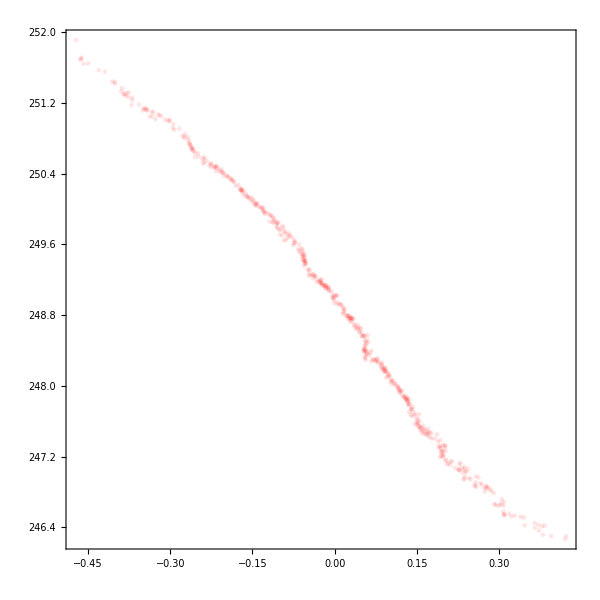

```mathematica
lplot=ListPlot[{Transpose[{10^12(z-Mean[z])/(2.99 10^8),10^-6 cpz}]},AspectRatio->1,Frame->True,ImageSize->600,PlotStyle->{{Red,Opacity[0.1]}}]
```

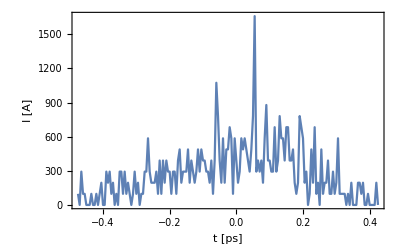

```mathematica
slicelength=0.005;
ListLinePlot[{#[[1]],Append[#[[2]],0]}//Transpose,Frame->True,PlotRange->{All,All},FrameLabel->{"t [ps]","I [A]"}]&[{1,250/(slicelength Length[#])}HistogramList[#,{slicelength}]]&[10^12(z-Mean[z])/(2.99 10^8)]
```

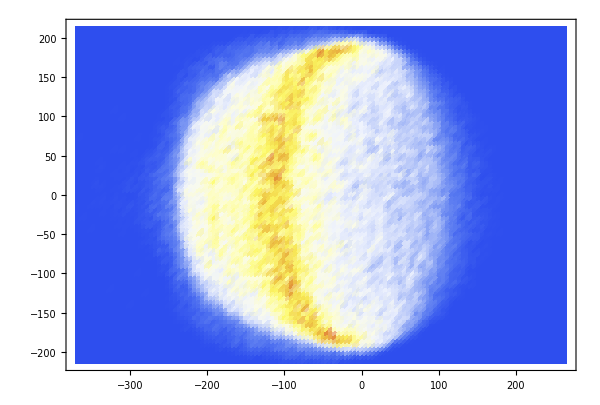

```mathematica
dplot=Block[{bins,hdata},
{bins,hdata}=HistogramList[10^6 Transpose[{x,y}],{100,100}];
ListDensityPlot[Transpose[hdata],AspectRatio->Automatic,ImageSize->600,DataRange->({#[[1]],#[[-1]]}&/@bins),Mesh->None,ColorFunction->(ColorData["TemperatureMap"])]]
```

## Plotting Emit Files

```mathematica
<<astrainterpret`
```

```mathematica
<<sddsBinaryinterpret`
```

```mathematica
SetDirectory["\\\\apclara1\\jkj62\\OnlineModel\\SimulationFramework\\Examples\\test"]
```

\\apclara1\jkj62\OnlineModel\SimulationFramework\Examples\test

```mathematica
ASTRAemitInterpret["./"~~#~~".Zemit.001"&/@{"L02","S03","L03","S04","L4H","S05","S06","L04","S07"},ASTRAVerbose->True]
```

Columns Redefined: z [m], t [ns], xavr [mm], xrms [mm], xprms [mrad], ϵxnorm [mm mrad π], xxpavr [mm mrad]

Columns Redefined: z [m], t [ns], yavr [mm], yrms [mm], yprms [mrad], ϵynorm [mm mrad π], yypavr [mm mrad]

Columns Redefined: z [m], t [ns], Ekin [MeV], zrms [mm], ΔErms [keV], ϵznorm [keV mm π], zEavr [keV]

```mathematica
sddsBinaryInterpret["./FEBE.sig",sddsVerbose->True]
```

Number of Pages: 1

Variables (Re)Assigned: {s, ElementName, ElementOccurence, ElementType, s1, s12, s13, s14, s15, s16, s17, s2, s23, s24, s25, s26, s27, s3, s34, s35, s36, s37, s4, s45, s46, s47, s5, s56, s57, s6, s67, s7, ma1, ma2, ma3, ma4, ma5, ma6, ma7, minimum1, minimum2, minimum3, minimum4, minimum5, minimum6, minimum7, maximum1, maximum2, maximum3, maximum4, maximum5, maximum6, maximum7, Sx, Sxp, Sy, Syp, Ss, Sdelta, St, ex, enx, ecx, ecnx, ey, eny, ecy, ecny, betaxBeam, alphaxBeam, betayBeam, alphayBeam}

Parameters (Re)Assigned: {Step}

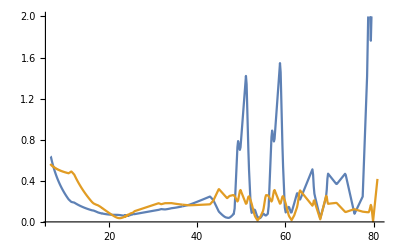

```mathematica
ListLinePlot[{Join[Transpose[{z,xrms}],Transpose[{s+Last[z],10^3 Sx}]],Join[Transpose[{z,yrms}],Transpose[{s+Last[z],10^3 Sy}]]},PlotRange->{All,{0,2}}]
```

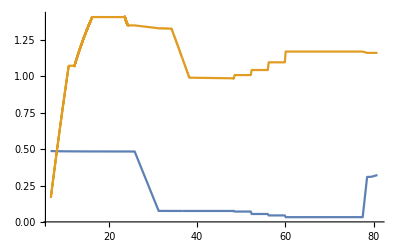

```mathematica
ListLinePlot[{Join[Transpose[{z,zrms}],Transpose[{s+Last[z],10^3 2.99 10^8 St}]],Join[Transpose[{z,10^-3 ΔErms}],Transpose[{s+Last[z],Ekin[[-1]] Sdelta}]]},PlotRange->All]
```

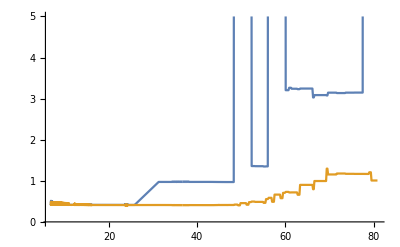

```mathematica
ListLinePlot[{Join[Transpose[{z,ϵxnorm}],Transpose[{s+Last[z],10^6 enx}]],Join[Transpose[{z,ϵynorm}],Transpose[{s+Last[z],10^6 eny}]]},PlotRange->{All,{0,5}}]
```

```mathematica
{x,y,z,cpx,cpy,cpz,t,q}=Transpose[Import["./CLA-FEB-W-FOCUS.hdf5","/beam/beam"]];
```

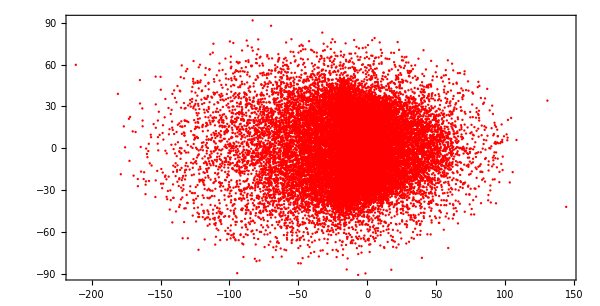

```mathematica
lplot=ListPlot[{10^6 Transpose[{x,y}][[1;;-1;;10]]},AspectRatio->Automatic,Frame->True,ImageSize->600,PlotStyle->{{Red}},PlotRange->All]
```

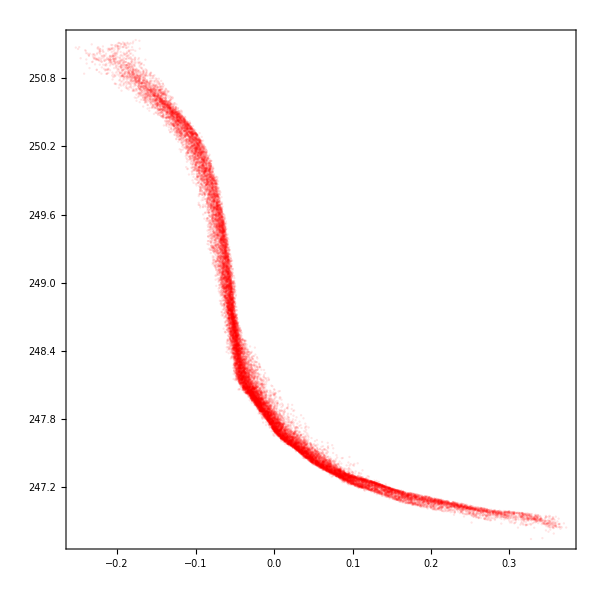

```mathematica
lplot=ListPlot[{Transpose[{10^12(z-Mean[z])/(2.98 10^8),10^-6 cpz}][[1;;-1;;10]]},AspectRatio->1,Frame->True,ImageSize->600,PlotStyle->{{Red,Opacity[0.1]}}]
```

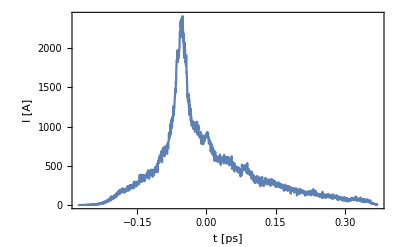

```mathematica
slicelength=0.0005;
ListLinePlot[{#[[1]],Append[#[[2]],0]}//Transpose,Frame->True,PlotRange->{All,All},FrameLabel->{"t [ps]","I [A]"}]&[{1,250/(slicelength Length[#])}HistogramList[#,{slicelength}]]&[10^12(z-Mean[z])/(2.99 10^8)]
```